```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Persistent

```mathematica
MakeCumulative[l0_]:=Module[{l=l0,t,i,s=0},
t=Tally[l];
Join[{{0,1}},Reap[For[i=1,i<Length[t],i++,
s+=t[[i]][[2]];
Sow[{t[[i]][[1]],1-s/Length[l]}];
]][[2]][[1]]]
]
```

## Packet Capture Rates

```mathematica
bitrateO=Transpose[Import["data1.udp53.br10.csv"]][[1]];
pktrateO=Transpose[Import["data1.udp53.pr10.csv"]][[1]];
```

```mathematica
bitrate=bitrateO[[;;-1000]];
pktrate=pktrateO[[;;-1000]];
```

```mathematica
tbitrate=Transpose[{
Table[10i,{i,0,Length[bitrate]-1}],
bitrate/8
}];
tpktrate=Transpose[{
Table[10i,{i,0,Length[pktrate]-1}],
pktrate/(8 10)
}];
```

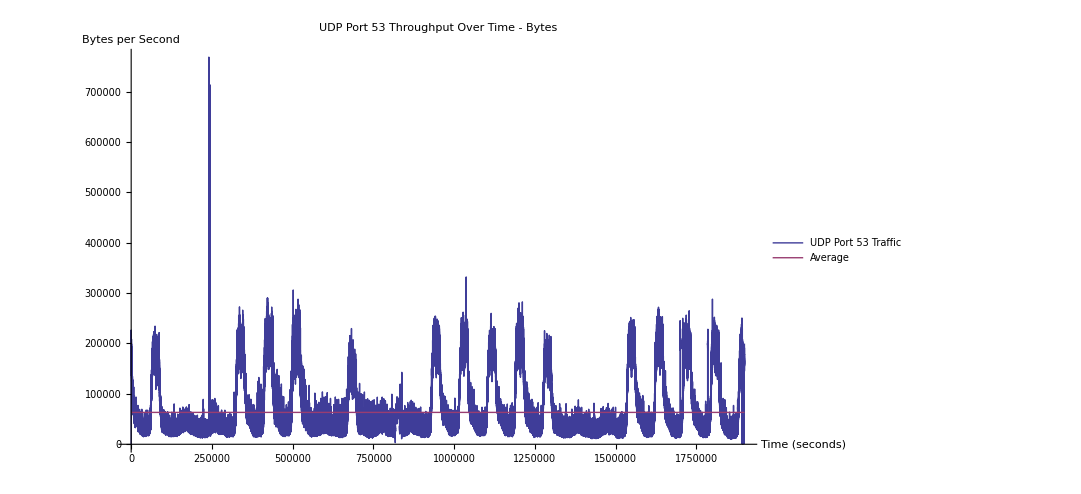

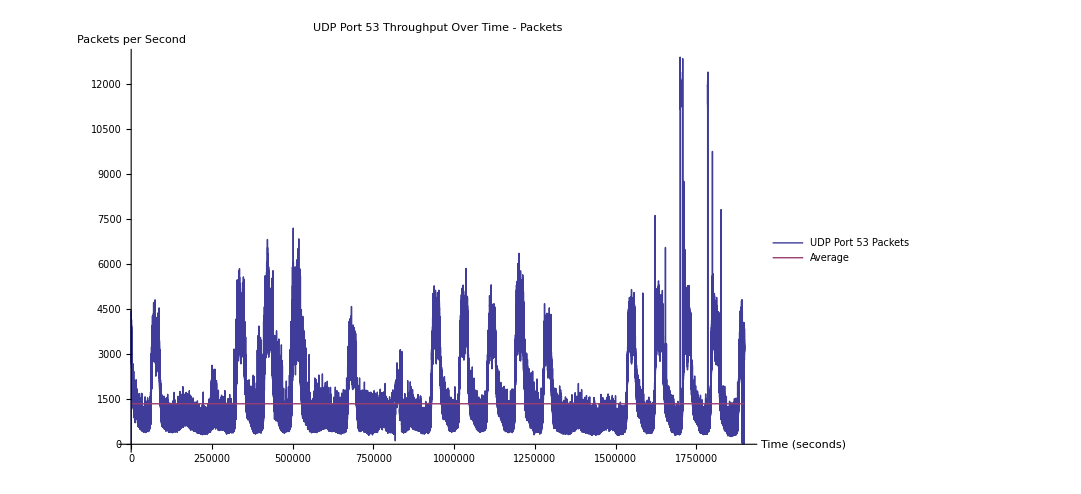

```mathematica
ListPlot[{tbitrate,{{0,Mean[bitrate]/8},{10Length[bitrate],Mean[bitrate]/8}}},Joined->True,PlotRange->All,PlotLegends->LineLegend[{"UDP Port 53\nTraffic","Average"}],ImageSize->800,PlotLabel->"UDP Port 53 Throughput Over Time - Bytes",AxesLabel->{"Time\n(seconds)","Bytes per Second"}]
ListPlot[{tpktrate,{{0,Mean[pktrate]/(8 10)},{10Length[pktrate],Mean[pktrate]/(8 10)}}},Joined->True,PlotRange->All,PlotLegends->LineLegend[{"UDP Port 53\nPackets","Average"}],ImageSize->800,PlotLabel->"UDP Port 53 Throughput Over Time - Packets",AxesLabel->{"Time\n(seconds)","Packets per Second"}]
```

```mathematica
Mean[bitrate]
```

508673.

## DNS Query Repetition

### Home

```mathematica
qhc=Import["query.log.home.sus.csv"][[1]]//MakeCumulative;//AbsoluteTiming
```

{5.82633,Null}

```mathematica
qhc={qhc[[All,1]]/(qhc[[All,1]]//Max),qhc[[All,2]]}//Transpose;//AbsoluteTiming
```

{0.,Null}

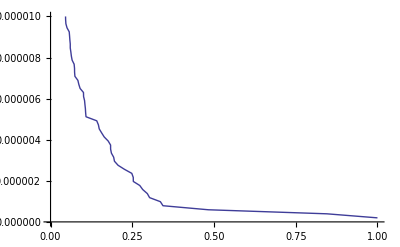

```mathematica
ListPlot[qhc,Joined->True,PlotStyle->Thick,PlotRange->{{0,1},{0,0.00001}}]
```

### Packet Capture

```mathematica
qpc=Import["q.big.queries\\q.big.q.sus.2.csv"][[1]]//MakeCumulative;//AbsoluteTiming
```

{26.50552,Null}

```mathematica
qpc={qpc[[All,1]]/(qpc[[All,1]]//Max),qpc[[All,2]]}//Transpose;//AbsoluteTiming
```

{0.01,Null}

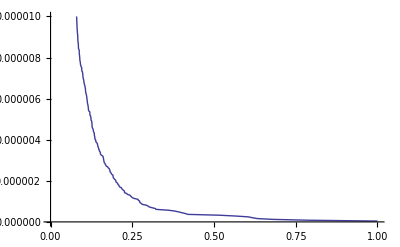

```mathematica
ListPlot[qpc,Joined->True,PlotStyle->Thick,PlotRange->{{0,1},{0,0.00001}}]
```

### Combined Plots

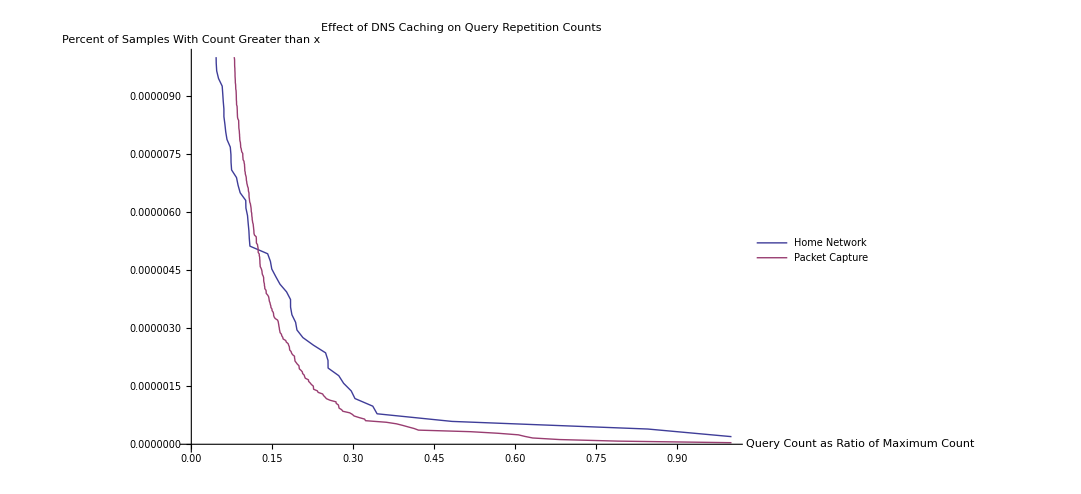

```mathematica
ListPlot[{qhc,qpc},Joined->True,PlotStyle->Thick,PlotRange->{{0,1},{0,0.00001}},PlotLegends->LineLegend[{"Home Network","Packet Capture"}],ImageSize->800,PlotLabel->"Effect of DNS Caching\non Query Repetition Counts",AxesLabel->{"Query Count as Ratio\nof Maximum Count","Percent of Samples With\nCount Greater than x"}]
```